# Facial Recognition using Eigenfaces

By Grant Timmerman and Danny Vance

## Section - Setting Up a Training Set

### First import the images we want to use

```mathematica
SetDirectory[StringJoin[NotebookDirectory[], "math_images_resized"]];
```

```mathematica
photos = Map[Import, {"f1.jpg","f2.jpg","f3.jpg","f4.jpg","f5.jpg","f6.jpg","f7.jpg","f8.jpg","f9.jpg","f10.jpg","f11.jpg","f12.jpg","f13.jpg","f14.jpg","f15.jpg","f16.jpg","f17.jpg","f18.jpg","f19.jpg","f20.jpg","f21.jpg","f22.jpg","f23.jpg", "f24.jpg", "f25.jpg"}]
numPhotos = Length[photos];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Next convert all the photos to grayscale

```mathematica
grayPhotos = Map[ColorConvert[#, "Grayscale"] &, photos]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Create useful methods for converting an image to a vector vice versa

```mathematica
imageToVector[img_] := Flatten[ImageData[img]];
imageSize = Sqrt[Dimensions[imageToVector[grayPhotos[[1]]]]]; (* Assumes the photo is square *)
vectorToImage[vec_] := Image[Partition[vec, Sqrt[Dimensions[vec][[1]]]]];
grayPhotosVector = Map[imageToVector, grayPhotos];
```

### (Optional) Display the images in a grid as a reference

```mathematica
grayPhotosMatrix = Transpose[Map[imageToVector,grayPhotos]];
```

```mathematica
grayPhotosGrid = Partition[grayPhotos, 5];
Grid[grayPhotosGrid, Spacings-> {0,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Section - Calculate the Mean and Difference Faces

### Calculating the mean face

```mathematica
meanFaceMatrix = Apply[Plus, Map[ImageData, grayPhotos]]/numPhotos;
meanFaceVector = Flatten[meanFaceMatrix];
meanFaceImage = Image[meanFaceMatrix]
```

-Graphics-

### Calculating the difference face and difference vectors

```mathematica
differenceFaces = Map[ImageSubtract[#, meanFaceImage] &, grayPhotos]
differenceVectors =Map[imageToVector, differenceFaces];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### (Optional) Display the images in a grid as a reference

```mathematica
(*displayedDifferencesFaces = 0;*)
getDisplayVector[vec_] := Module[
{},
Map[.5 +.5# &,vec]
];
displayDifferenceVectors = Map[getDisplayVector[#] &, differenceVectors];
displayDifferenceFaces = Map[vectorToImage, displayDifferenceVectors];
differenceFacesGrid = Partition[displayDifferenceFaces, 5];
Grid[differenceFacesGrid, Spacings-> {0,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### The difference vector of the mean face:

```mathematica
vectorToImage[getDisplayVector[meanFaceVector - meanFaceVector]]
```

-Graphics-

## Section - Finding Eigenfaces

### Find the small matrix

```mathematica
babyMatrix = differenceVectors.Transpose[differenceVectors];
```

### Choose a fixed number of eigenfaces and diagonalize the eigenvectors of the normalized small matrix

```mathematica
numEigenFaces = numPhotos;
```

```mathematica
eigenfaceSystem=Eigensystem[babyMatrix];
eigenfaces=Map[Normalize[Transpose[differenceVectors].#]&,eigenfaceSystem⟦2⟧];
diagonalCovarianceMatrix=DiagonalMatrix[eigenfaceSystem⟦1⟧];
```

### (Optional) Display the images in a grid as a reference

```mathematica
getEigenfaceDisplayVector[vec_] := Module[{},
Map[.5 +25# &,vec]
];
displayEigenfaces = Map[vectorToImage[getEigenfaceDisplayVector[#]] &,eigenfaces];
Grid[Partition[displayEigenfaces, 5], Spacings-> {0,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Section - Project Images into the Eigenspace

### Define a function that projects an image to the eigenspace

```mathematica
projectImageToFaceSpace[imageVector_,meanFaceVector_, eigenfaces_]:=
Module[{differenceVector},
differenceVector=imageVector-meanFaceVector;
Map[differenceVector.#&,eigenfaces]
];
```

### Calculate the eigenface coefficients for each face you wish to project

```mathematica
(* A set of eigenface coefficients for each face *)
eigenfaceCoefficients = Map[projectImageToFaceSpace[#, meanFaceVector, eigenfaces]&, grayPhotosVector];
```

## Section - Recontruct Images from Eigenspace

### Define a function that reconstructs a face vector from eigenface coefficients

```mathematica
rebuildVectorFromEigenfaces[coefficients_, meanFaceVector_,eigenfaces_, numEigenfaces_]:=
meanFaceVector+Apply[Plus,(coefficients*eigenfaces)⟦;;numEigenfaces⟧];
```

### Reconstruct some training set faces

```mathematica
randomFaces = Map[vectorToImage,{rebuildVectorFromEigenfaces[eigenfaceCoefficients[[5]],meanFaceVector,eigenfaces,3],rebuildVectorFromEigenfaces[eigenfaceCoefficients[[23]],meanFaceVector,eigenfaces,24],rebuildVectorFromEigenfaces[eigenfaceCoefficients[[3]],meanFaceVector,eigenfaces,13],rebuildVectorFromEigenfaces[eigenfaceCoefficients[[12]],meanFaceVector,eigenfaces,6],rebuildVectorFromEigenfaces[eigenfaceCoefficients[[24]],meanFaceVector,eigenfaces,1],rebuildVectorFromEigenfaces[eigenfaceCoefficients[[2]],meanFaceVector,eigenfaces,22]}];
Grid[Partition[randomFaces,Length[randomFaces]/2], Spacings->{0,0}]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
reconstructedTrainingFaces = Table[
Table[
ImageResize[
vectorToImage[
rebuildVectorFromEigenfaces[eigenfaceCoefficients[[photoNum]], meanFaceVector, eigenfaces, numEigenfaces]
],{40}],
 {numEigenfaces, numPhotos}],
{photoNum, numPhotos}
];
Grid[reconstructedTrainingFaces, Spacings-> {0,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Reconstruct some faces not in training set

```mathematica
otherPhotos = Map[Import, {"fb1.jpg","fb2.jpg", "fb3.jpg", "fb4.jpg", "orangutan.jpg", "steven.jpg", "kirby.jpg", "flower.jpg"}];
numOtherPhotos = Length[otherPhotos];
otherGrayPhotos = Map[ColorConvert[#, "Grayscale"] &, otherPhotos];
Grid[Partition[otherGrayPhotos,Length[otherPhotos]], Spacings->{0,0}]
otherGrayPhotosVector = Map[imageToVector, otherGrayPhotos];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
otherEigenfaceCoefficients = Map[projectImageToFaceSpace[#, meanFaceVector, eigenfaces]&, otherGrayPhotosVector];
imageSize = 50;
otherReconstructedFaces =
Table[
Table[
ImageResize[
vectorToImage[
rebuildVectorFromEigenfaces[otherEigenfaceCoefficients[[photoNum]], meanFaceVector, eigenfaces, numEigenfaces]
],{imageSize}],
 {numEigenfaces, numPhotos}],
{photoNum, numOtherPhotos}
];
{Grid[otherReconstructedFaces, Spacings-> {0,0}], Grid[Partition[Map[ImageResize[#,{imageSize}]&,otherGrayPhotos],1], Spacings->{0,0}]}
```

{-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-}

```mathematica
Grid[{otherGrayPhotos,
Table[vectorToImage[rebuildVectorFromEigenfaces[otherEigenfaceCoefficients[[photoNum]], meanFaceVector, eigenfaces, numPhotos]],{photoNum, numOtherPhotos}]}, Spacings->{0,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Section - Measure Reconstruction Accuracy

### Define a function that gets the difference between two image vectors

```mathematica
getImageVectorDifference[imageVector1_,imageVector2_]:= 
Module[{differenceVector},
differenceVector = imageVector1-imageVector2;
Total@Abs@differenceVector/Times@@Dimensions@imageVector1*100
];
```

### Calculate the differences between the normal images and the reconstructed images

```mathematica
imgNum= 21;
imgSize = 50;
accuracyTable = {
Table[ImageResize[grayPhotos[[imgNum]],imgSize], {i,0, 25}],
Table[ImageResize[vectorToImage[rebuildVectorFromEigenfaces[eigenfaceCoefficients[[imgNum]], meanFaceVector, eigenfaces, numEigenfaces]],imgSize],{numEigenfaces,0, 25}],
Table[StringJoin[
"\n",
ToString[
NumberForm[getImageVectorDifference[grayPhotosVector[[imgNum]], rebuildVectorFromEigenfaces[eigenfaceCoefficients[[imgNum]], meanFaceVector, eigenfaces, i]],2]
],
"%"], {i,0, 25}]
};
Grid[accuracyTable, Spacings-> {0,0}];
getAccuracyTable[imageVectors1_,imageVectors2_] := Module[
{},
{
Map[vectorToImage,imageVectors1],
Map[vectorToImage,imageVectors2],
Table[
StringJoin[
"\n",
ToString[
NumberForm[getImageVectorDifference[imageVectors1[[1]],imageVectors2[[i]]],2]
],
"%"], {i,1, 25}
]
}
];
```

### Graph the accuracy over number of applied eigenfaces

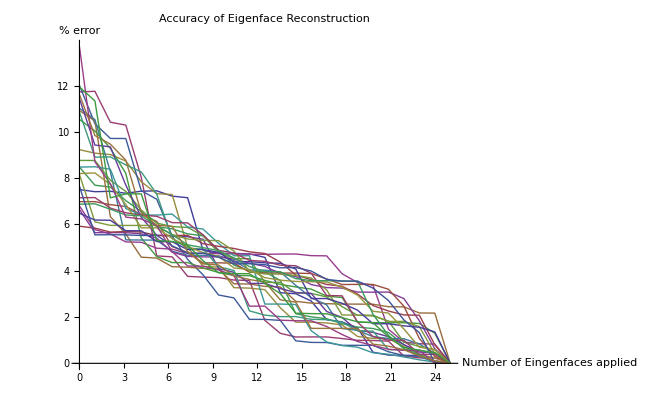

```mathematica
diffs = Table[Table[getImageVectorDifference[grayPhotosVector[[faceNum]], rebuildVectorFromEigenfaces[eigenfaceCoefficients[[faceNum]], meanFaceVector, eigenfaces, numEigenfaces]], {numEigenfaces, 0, 24}], {faceNum,1, 25}];
faceNum = 2;
ListPlot[diffs, Joined->True, InterpolationOrder->1, DataRange->{0, 25}, PlotLabel->"Accuracy of Eigenface Reconstruction",AxesLabel-> {"Number of\nEingenfaces applied", "% error"}]
```

## Section - Facial Recognition

### To recognize a face in the training set, we seek the training set image with the minimum variance with the reconstructed image

```mathematica
getPercentMatches[imgNum_, numEigenfaces_] := Module[{},
inputVector = rebuildVectorFromEigenfaces[eigenfaceCoefficients[[imgNum]], meanFaceVector, eigenfaces, numEigenfaces];
differencePercentagesBetweenFaces = Table[getImageVectorDifference[grayPhotosVector[[i]],inputVector],  {i, 25}];
sortedOrder = Sort[differencePercentagesBetweenFaces]
];
getMatchedPhotos[matchOrder_] := Module[{},
Table[grayPhotos[[Position[differencePercentagesBetweenFaces, sortedOrder[[i]]][[1,1]]]], {i, 25}]
];
getPercentMatchesOther[imgNum_, numEigenfaces_] := Module[{},
inputVector = rebuildVectorFromEigenfaces[otherEigenfaceCoefficients[[imgNum]], meanFaceVector, eigenfaces, numEigenfaces];
differencePercentagesBetweenFaces = Table[getImageVectorDifference[grayPhotosVector[[i]],inputVector],  {i, 25}];
sortedOrder = Sort[differencePercentagesBetweenFaces]
];
```

### (Optional) Create a grid that shows the order of the face matches

```mathematica
Style[Grid[Partition[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25},5], Frame->All], FontSize-> 60]
```

1 | 2 | 3 | 4 | 5
6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15
16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25

### Recognize Training Faces

#### Choose a face number (faceNum) from the training faces set and number of eigenfaces to apply (numEigen) to recreate the face

-Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

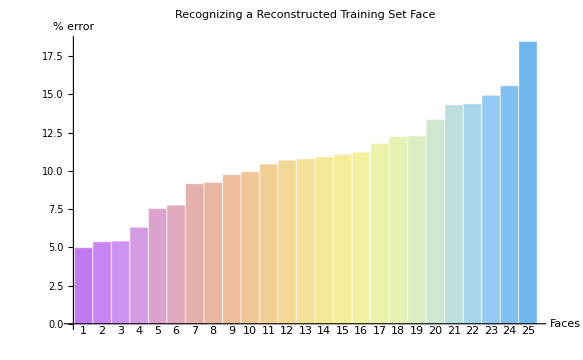

```mathematica
faceNum = 16;
numEigen = 8;
recreatedPhoto = vectorToImage[rebuildVectorFromEigenfaces[eigenfaceCoefficients[[faceNum]], meanFaceVector, eigenfaces, numEigen]];
Grid[{{grayPhotos[[faceNum]],recreatedPhoto}},Spacings->{0,0}]
order = getPercentMatches[faceNum, numEigen];
Grid[Partition[getMatchedPhotos[order],5],Spacings->{0,0}]
SetOptions[BarChart,BaseStyle->{FontFamily->"Times",FontSize->14}];
BarChart[order, ChartStyle->"Pastel", AxesLabel-> {"Faces", "% error"},PlotLabel-> "Recognizing a Reconstructed Training Set Face", ChartLabels->{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25"}]
```

### Results of Recognizing Training Faces

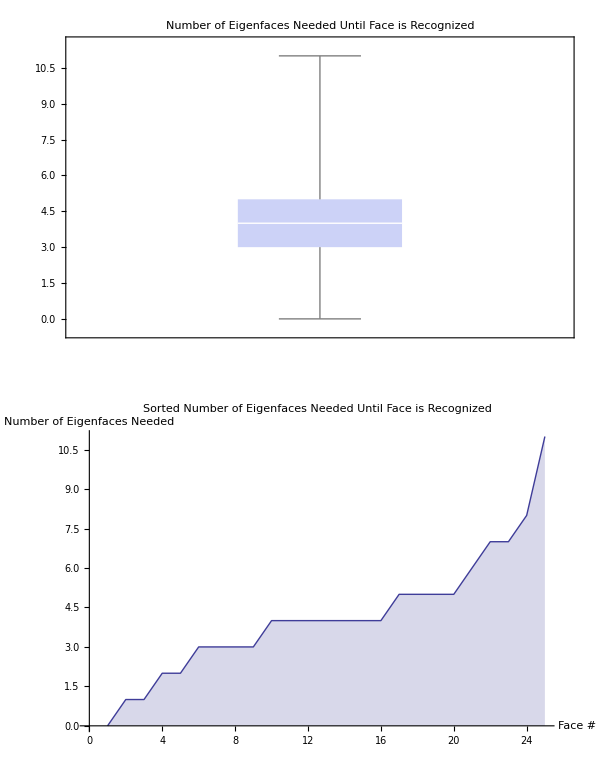

```mathematica
numEigenToRecognize = {8, 5, 7, 3, 4, 3, 2, 4, 2, 5, 6, 4, 4, 4, 0, 11, 4, 3, 5, 3, 7, 1, 1, 4, 5};
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
SetOptions[BoxWhiskerChart,BaseStyle->{FontFamily->"Times",FontSize->14}];
GraphicsGrid[{{BoxWhiskerChart[numEigenToRecognize, PlotLabel->"Number of Eigenfaces Needed Until Face is Recognized"]},
{ListPlot[Sort[numEigenToRecognize], Filling->Axis, PlotStyle->{Thick, PointSize[Large]}, Joined->True,  PlotLabel->"Sorted Number of Eigenfaces Needed Until Face is Recognized", AxesLabel->{"Face #","Number of \nEigenfaces Needed"}]}}]
```

### Recognizing Foreign Faces

#### Choose a face number (faceNum) from the foreign faces set and number of eigenfaces to apply (numEigen) to recreate the face

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

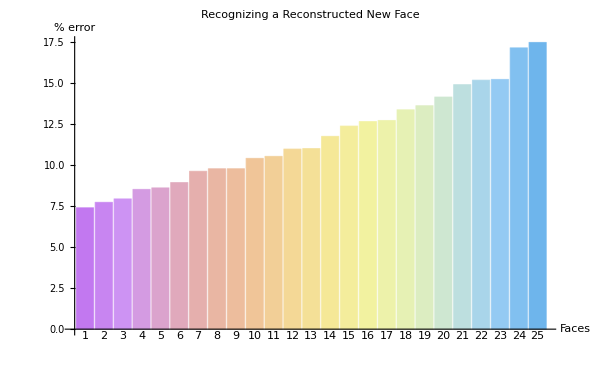

```mathematica
faceNum = 8;
numEigen = 24;
recreatedPhotos = Table[vectorToImage[rebuildVectorFromEigenfaces[otherEigenfaceCoefficients[[i]], meanFaceVector, eigenfaces, numEigen]],{i,numOtherPhotos}];
{otherGrayPhotos[[faceNum]], recreatedPhotos[[faceNum]]};
order =getPercentMatchesOther[faceNum, numEigen];
getMatchedPhotos[order]

BarChart[order, ChartStyle->"Pastel", AxesLabel-> {"Faces", "% error"},PlotLabel-> "Recognizing a Reconstructed New Face", ChartLabels->{"1","2","3","4","5","6","7","8","9","10","11","12","13","14","15","16","17","18","19","20","21","22","23","24","25"}]
```

### Results of Recognizing Foreign Faces

```mathematica
t = Table[{Grid[{{otherGrayPhotos[[i]],recreatedPhotos[[i]]}}, Spacings->{0,0}],Grid[{getMatchedPhotos[getPercentMatchesOther[i, 24]][[1;;5]]},Spacings->{0,0}]},{i,8}];
Grid[t, Spacings->{2,0}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## (Optional) Face Visualizations

### Mean Face Luminosity Visualization

```mathematica
imgSize = 40;
ListPlot3D[Partition[imageToVector[ImageResize[meanFaceImage, {imgSize,imgSize}]], imgSize], Mesh -> All]
```

-Graphics3D-

### Face Luminosity Visualization

```mathematica
density = 60;
picNum = 9;
alpha = 1;
blurValue = 0;
colorData = ImageData[Blur[ImageResize[photos[[picNum]], {density, density}],blurValue]];

getColor[x0_, y0_] := Module[
{x=x0,y=y0},
y *= density;
x *= density;
If[y < 1, y = 1,];
If[x < 1, x = 1,];
If[y > density, RGBColor[0,0,0, alpha],If[x > density , RGBColor[0,0,0, alpha],pictureColor[Round[x],Round[y]]]]
];

pictureColor[x_,y_] := RGBColor[colorData[[x]][[y]][[1]], colorData[[x]][[y]][[2]], colorData[[x]][[y]][[3]], alpha];
resizeImage[i_] :=  Blur[ImageResize[grayPhotos[[i]], {density,density}], blurValue];
getImageVector[i_] :=Transpose[Partition[imageToVector[resizeImage[i]],density]];

v1[i_] :=ListPlot3D[{getImageVector[i]}, Mesh -> None, InterpolationOrder -> 1, ColorFunction -> Function[{x, y, z},getColor[x,y]]];
v2[i_] :=ListPointPlot3D[{getImageVector[i]}, ColorFunction -> Function[{x, y, z},getColor[x,y]], BoxRatios -> {1,1,.5}, PlotStyle-> PointSize[Large]];
v3[i_] :=ListPlot3D[{getImageVector[i]}, InterpolationOrder -> 0, ColorFunction -> Function[{x, y, z},getColor[x,y]], Mesh -> None, BoundaryStyle->None];
v4[i_] := DiscretePlot3D[getImageVector[i][[k]][[j]],{j, 1, density}, {k, 1, density}, ColorFunction -> Function[{x, y,z},getColor[x,y]], ExtentSize->Full,PlotStyle->EdgeForm[], ExtentElementFunction -> "Cube"]
```

```mathematica
v4[picNum]
```

-Graphics3D-

### Animations

```mathematica
(*Export["/animation.gif",Table[rebuildFromEigenfaces[coefficients, meanImage, eigenfaces, k], {k, 1, 25}],"GIF"];*)
```